```mathematica
g=9.8; (*grav. constant*)
l=0.5; (*length of pendulum*)

θ0=20*π/180; (*20 degrees*)
ω0 = 0; (*starting from rest*)
(*ϕ=y;
t=x;*)
ode1={θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0};
sol=NDSolve[ode1,θ,{t,0,20}];
```

```mathematica
myplot1 = Plot[(180/Pi) θ[t]/.sol,{t,0,20},PlotStyle-> RGBColor[0,0,1],PlotRange-> All];
omega=√(g/l);
```

```mathematica
approx = (180/Pi) θ0 Cos[omega*t];
myplot2=Plot[approx,{t,0,20},PlotStyle-> RGBColor[1,0,0],PlotRange-> All];
```

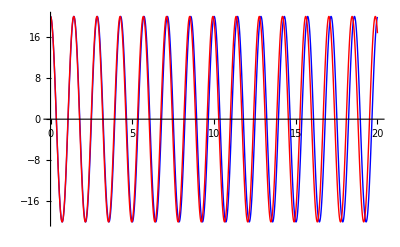

```mathematica
Show[{myplot1,myplot2}]
```

```mathematica
g=9.8;
V =30;
ode1 ={x''[t] == (-g  x'[t]/vt^2)Sqrt[x'[t]^2 +y'[t]^2],
y''[t] ==-g (1 + (y'[t]/vt^2)Sqrt[x'[t]^2 + y'[t]^2]), x[0] == 0,y[0] == 2, x'[0] = V *Cos[50 *(π/180)],y'[0] == V * Sin[50 *(π/180)]}
```

{x''[t]==-(9.8 x'[t] √(x'[t]^2+y'[t]^2))/vt^2,y''[t]==-9.8 (1+(y'[t] √(x'[t]^2+y'[t]^2))/vt^2),x[0]==0,y[0]==2,30 Sin[(2 π)/9],y'[0]==30 Cos[(2 π)/9]}

```mathematica
sol=NDSolve[ode1,{x,y},{t,0,200}];*)
```

NDSolve::deqn: Equation or list of equations expected instead of 30\ Sin[2\ π/9] in the first argument SuperscriptBox[SuperscriptBox[x[0] == 0y[0] == 230 Sin[2 π/9]SuperscriptBox[.

```mathematica
Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tf}, PlotRange->
(*g=9.8; l=0.5; omega=√(g/l);
Module[
{result = NDSolve[{θ''[t]==-(g/l)*Sin[θ[t]],θ[0]==θ0,θ'[0]==ω0},θ, {t, 0,20}]},
Plot[{(180/Pi) θ0 Cos[omega*t],(180/Pi)* θ[t]/.result},{t,0,20},PlotStyle-> {{Blue},{Dashed,Red}},PlotRange-> All,AxesLabel->{"t (s)","θ (rad)"},PlotRange->{{0,20},{-20,20}},ImageSize->{500,300}]],
{{l,0.5,"length (m)"},0,2,Appearance->"Labeled"},{{θ0,20*Pi/180,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{ω0,0,"initial speed (rad/s)"},0,10.,Appearance->"Labeled"}]*)
```

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.803041, False}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.803041, False}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.803041, False}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.803041, False}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsfun: 5\ π/18 cannot be used as a function.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[(5 π/18),  is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

ReplaceAll::reps: {NDSolve[{0 == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.803041, False}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.000408571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: {NDSolve[{0. == -19.6\ Sin[0.872665[0.000408571]], 0.872665[0.] == 0.803041, False}, 0.872665, {0.000408571, 0., 20.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

```mathematica
g=9.8;
V =30;
θ = 50 *(π/180);
vt =100;
ode1 = {x''[t] == (-gx'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g(1+(y'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0] ==2,x'[0]==V*Cos[θ],y'[0] ==V*Sin[θ]};
(*ode1 ={x''[t] == (-g  x'[t]/vt^2)Sqrt[x'[t]^2 +y'[t]^2],y''[t] ==-g (1 + (y'[t]/vt^2)Sqrt[x'[t]^2 + y'[t]^2]), x[0] == 0,y[0] == 2, x'[0] = V *Cos[θ],y'[0] == V * Sin[θ]}*)

sol=NDSolve[{x''[t] == (-gx'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g(1+(y'[t]/vt^2)Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0] ==2,x'[0]==V*Cos[θ],y'[0] ==V*Sin[θ]},{x,y},{t,0,200}]
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,60},PlotRange->{{0,100},{0,60}}]
(*ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tf},{{tf,0.01,"time (s)"},0.01,100},PlotRange->{{0,100},{0,60}}]*)
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument SuperscriptBox[SuperscriptBox[x[0] == 0y[0] == 2TrueSuperscriptBox[.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00122449 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00122449 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 1.22571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-

```mathematica
g=9.8 (*m/s^2*);
v=30;
θ=50 π/180;

ode1={x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==2,x'[0]==v*Cos[θ],y'[0]==v*Sin[θ]};
sol=NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==2,x'[0]==v*Cos[θ],y'[0]==v*Sin[θ]},{x,y},{t,0,200}];
ParametricPlot[Evaluate[{x[t],y[t]}/.NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==2,x'[0]==v*Cos[θ],y'[0]==v*Sin[θ]},{x,y},{t,0,200}]],{t,0,200},PlotRange->{{0,100},{0,60}}]

Manipulate[ParametricPlot[Evaluate[{x[t],y[t]}/.NDSolve[{x''[t]==(-g x'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2],y''[t]==-g (1+(y'[t]/vt^2) Sqrt[x'[t]^2+y'[t]^2]),x[0]==0,y[0]==z,x'[0]==v*Cos[θ],y'[0]==v*Sin[θ]},{x,y},{t,0,200}]],{t,0,tf},PlotRange->{{0,100},{0,60}}],{{tf,0.01,"time(s)"},0.01,10,Appearance->"Labeled"},{{v,10,"Velocity(m/s)"},0.01,100,Appearance->"Labeled"},{{g,9.8,"Gravity(m/s^s"},0.01,50,Appearance->"Labeled"},{{vt,10,"Terminal Velocity(m/s)"},1.0,200,Appearance->"Labeled"},{{z,0,"Starting Height(m)"},0.0,5,Appearance->"Labeled"},{{θ,50 Pi/180,"θ(rad/s)"},0.01,π,Appearance->"Labeled"}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00408163 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 0.00408163 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 4.08571 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

-Graphics-